# Determinación T_c α=1

```mathematica
f[x_,a_,b_,c_,d_] :=a*x^3+b*x^2+c*x+d
```

## L=032

```mathematica
a32 := -185.763172530113
b32 := 1255.73006086081
c32 := -2830.40066015888
d32 := 2127.85521102121
```

## L=064

```mathematica
a64 := -206.383286315853
b64 := 1367.79915149397
c64 := -3021.64260834708
d64 := 225.6871771717
```

## L=128

```mathematica
a128 := -315.460653488358
b128 := 2024.47456246018
c128 := -4319.13624512509
d128:= 3063.10071275729
```

## L=256

```mathematica
a256 := 5991.29939374408
b256 := -40962.8345093221
c256 := 93340.5631233541
d256:= -70885.8925068051
```

## L=512

```mathematica
a512 := 25935.2469094999
b512 :=-176688.189183087
c512 :=401216.492557329
d512 := -303671.152278882
```

#### Entre L=128 y L=064

{{x→0.677264-2.26199 ⅈ},{x→0.677264+2.26199 ⅈ},{x→4.66574}}

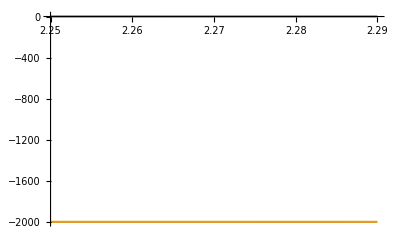

```mathematica
Solve[f[x,a128,b128,c128,d128]==f[x,a64,b64,c64,d64],x]
Plot[{f[x,a128,b128,c128,d128],f[x,a64,b64,c64,d64]},{x,2.25,2.29}]
```

#### Entre L=064 y L=032

{{x→-2.827},{x→4.13097-3.9454 ⅈ},{x→4.13097+3.9454 ⅈ}}

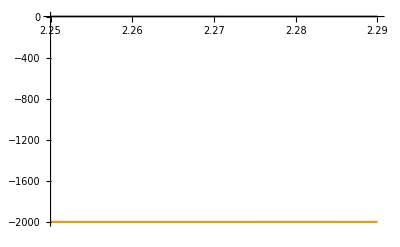

```mathematica
Solve[f[x,a64,b64,c64,d64]==f[x,a32,b32,c32,d32],x]
Plot[{f[x,a32,b32,c32,d32],f[x,a64,b64,c64,d64]},{x,2.25,2.29}]
```

## Entre L=256 y L=128

{{x→2.24464},{x→2.25783},{x→2.3136}}

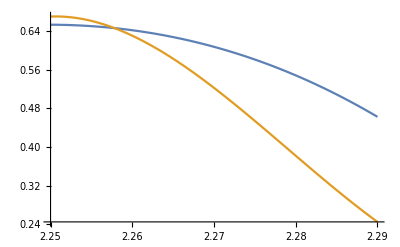

```mathematica
Solve[f[x,a128,b128,c128,d128]==f[x,a256,b256,c256,d256],x]
Plot[{f[x,a128,b128,c128,d128],f[x,a256,b256,c256,d256]},{x,2.25,2.29}]
```

## Entre L=512 y L=256

{{x→0.+0. ⅈ},{x→3.40267-1.96441 ⅈ},{x→3.40267+1.96441 ⅈ}}

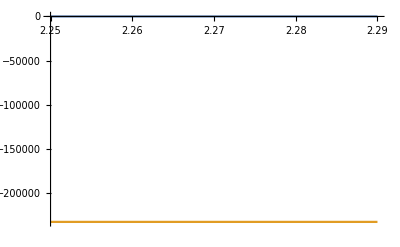

```mathematica
Solve[f[x,a512,b512,c512,d512]==f[x,a256,b256,c256,d512],x]
Plot[{f[x,a512,b512,c512,d512],f[x,a256,b256,c256,d512]},{x,2.25,2.29}]
```

## Ajuste Lineal

```mathematica
g[x_,d_,e_] := d*x+e
```

## L=32

```mathematica
d32:=-8.11197
e32:=2.45083
```

## L=64

```mathematica
d64:= -14.8882
e64:= 3.98481
```

## L=128

```mathematica
d128:= -38.2895
e128:=9.29327
```

## L=256

```mathematica
d256:=-105.742
e256:=24.5914
```

## L=512

```mathematica
d512:=-191.063
e512:=43.9446
```

### Entre L=32 y L=64

{{x→0.226377}}

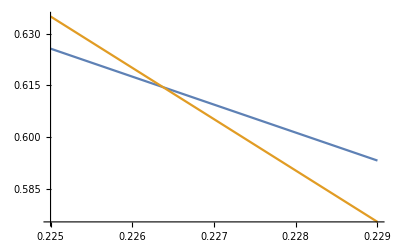

```mathematica
Solve[g[x,d64,e64]==g[x,d32,e32],x]
Plot[{g[x,d32,e32],g[x,d64,e64]},{x,0.225,0.229}]
```

### Entre L=64 y L=128

{{x→0.226845}}

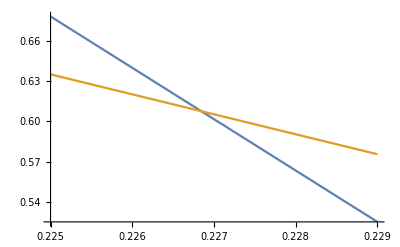

```mathematica
Solve[g[x,d64,e64]==g[x,d128,e128],x]
Plot[{g[x,d128,e128],g[x,d64,e64]},{x,0.225,0.229}]
```

### Entre L=128 y L=256

{{x→0.226799}}

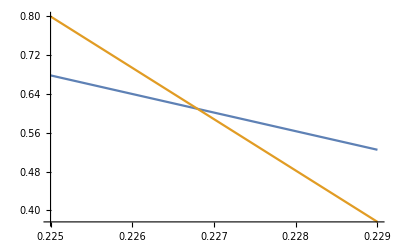

```mathematica
Solve[g[x,d256,e256]==g[x,d128,e128],x]
Plot[{g[x,d128,e128],g[x,d256,e256]},{x,0.225,0.229}]
```

### Entre L=256 y L=512

{{x→0.226828}}

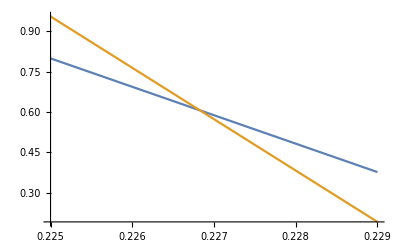

```mathematica
Solve[g[x,d256,e256]==g[x,d512,e512],x]
Plot[{g[x,d256,e256],g[x,d512,e512]},{x,0.225,0.229}]
```